## Midpoint-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 21:19:24
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
```

```mathematica
edge1={polygon[[1]], polygon[[2]]}
```

{{0.665682,0.588514},{0.367427,0.548792}}

```mathematica
MidPoint[edge1]
```

{0.516554,0.568653}

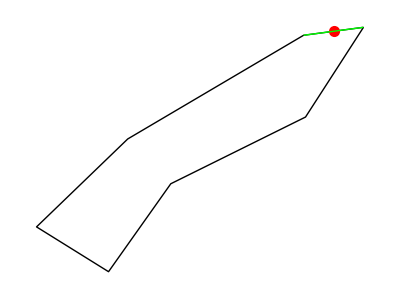

```mathematica
Show[Boundary[polygon], Graphics[{
Red, PointSize[.02], Point[MidPoint[edge1]],
 Thick, Green, Line[edge1]}]
]
```

```mathematica
allmidpoints=MidPoint[polygon]
```

{{0.516554,0.568653},{-0.0704379,0.2904},{-0.735411,-0.187169},{-0.783232,-0.51799},{-0.448916,-0.41049},{0.0416231,-0.0250531},{0.521407,0.364877}}

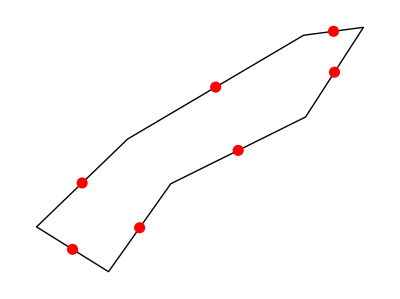

```mathematica
Show[Boundary[polygon], Graphics[{
Red, PointSize[.02], Sequence@@(Point/@allmidpoints)}]
]
```

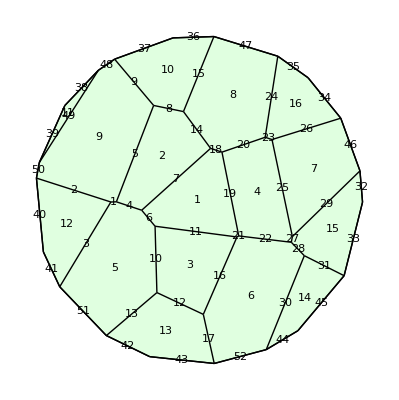

```mathematica
w=TemplateRandomCircularGrid[16,100];
ShowTissue[w, "CellNumbers"-> True, "EdgeNumbers"-> True]
```

```mathematica
MidPoint[w,2]
```

{{-42.5748,-3.656},{-13.8163,12.6245},{-1.0679,42.6653},{-18.4524,55.7284},{-38.9312,28.2483}}

```mathematica
MidPoint[w,2,3]
```

{-1.0679,42.6653}

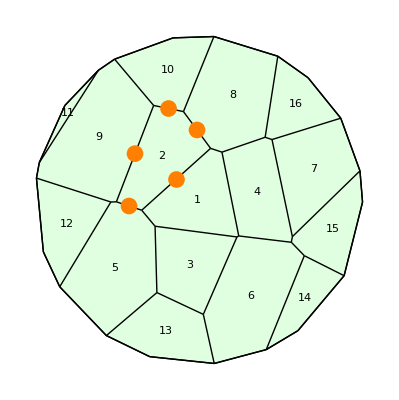

```mathematica
Show[ShowTissue[w, "CellNumbers"-> True], 
Graphics[{Orange,PointSize[.03],Point/@MidPoint[w,2]}]]
```